```mathematica
Guy F. Mongelli                                                              ECHE 462
```

```mathematica
Prof. R.M. Sankaran                                                   4/12/2013
```

```mathematica
Assignment #5
```

```mathematica
Problem 3:
```

```mathematica
Part B:
```

```mathematica
FOR THE LINEAR REGRESSION CASE:
```

```mathematica
The first data set corresponds the turnover rate (1/s)to PCO(torr):
```

```mathematica
RAWdata={{30.4,.00503},{30.4,0.00906},{30.4,.0184},{30.4,.0227}, {30.4,.0361},{7.6,.0386},{15.2,.0239},{45.6,.0117},{76,.00777}};
```

```mathematica
The second data set corresponds  the turnover rate (1/s) to PN2O (torr):
```

```mathematica
RAWdata2={{7.6,.00503},{15.2,0.00906},{30.4,.0184},{45.6,.0227}, {76,.0361},{30.4,.0386},{30.4,.0239},{30.4,.0117},{30.4,.00777}};
```

```mathematica
Next, the data must be manipulated to fit into the following expression:
```

```mathematica
Pn/r=1/k1+k2/k1 Pn+k2/k2 Pc
```

```mathematica
Let Pn/r be denoted simply as y.
```

```mathematica
PCO[1]=PCO[2]=PCO[3]=PCO[4]=PCO[5]=30.4;
```

```mathematica
PCO[6]=7.6;
```

```mathematica
PCO[7]=15.2;
```

```mathematica
PCO[8]=45.6;
```

```mathematica
PCO[9]=76;
```

```mathematica
PNO[1]=7.6;
```

```mathematica
PNO[2]=15.2;
```

```mathematica
PNO[3]=30.4;
```

```mathematica
PNO[4]=45.6;
```

```mathematica
PNO[5]=76;
```

```mathematica
PNO[6]=PNO[7]=PNO[8]=PNO[9]=30.4;
```

```mathematica
r[1]=.00503;
```

```mathematica
r[2]=.00906;
```

```mathematica
r[3]=.0184;
```

```mathematica
r[4]=.0227;
```

```mathematica
r[5]=.0361;
```

```mathematica
r[6]=.0386;
```

```mathematica
r[7]=.0239;
```

```mathematica
r[8]=.0117;
```

```mathematica
r[9]=.00777;
```

```mathematica
y[n_]=PNO[n]/r[n]
```

PNO[n]/r[n]

```mathematica
data={{PNO[1],r[1]},{PNO[2],r[2]},{PNO[3],r[3]},{PNO[4],r[4]},{PNO[5],r[5]},{PNO[6],r[6]},{PNO[7],r[7]},{PNO[8],r[8]},{PNO[9],r[9]}}
```

{{7.6,0.00503},{15.2,0.00906},{30.4,0.0184},{45.6,0.0227},{76,0.0361},{30.4,0.0386},{30.4,0.0239},{30.4,0.0117},{30.4,0.00777}}

```mathematica
data2={{PCO[1],r[1]},{PCO[2],r[2]},{PCO[3],r[3]},{PCO[4],r[4]},{PCO[5],r[5]},{PCO[6],r[6]},{PCO[7],r[7]},{PCO[8],r[8]},{PCO[9],r[9]}}
```

{{30.4,0.00503},{30.4,0.00906},{30.4,0.0184},{30.4,0.0227},{30.4,0.0361},{7.6,0.0386},{15.2,0.0239},{45.6,0.0117},{76,0.00777}}

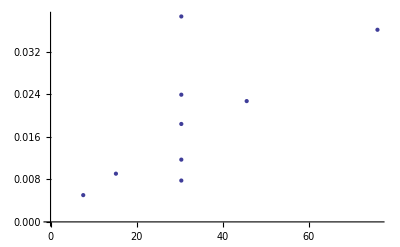

```mathematica
ListPlot[data]
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[0.00499806+0.000432785 x]

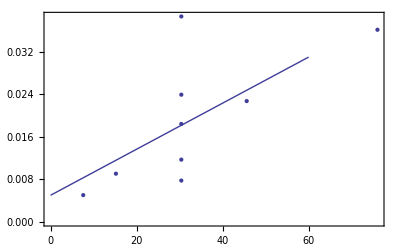

```mathematica
Show[ListPlot[data],Plot[lm[x],{x,0,60}],Frame->True]
```

```mathematica
The R-squared value associated with the linear fit to the data set is:
```

```mathematica
lm["RSquared"]
```

0.47377

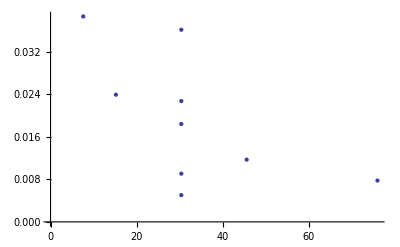

```mathematica
ListPlot[data2]
```

```mathematica
lm2=LinearModelFit[data2,x,x]
```

FittedModel[0.0318622-0.000382928 x]

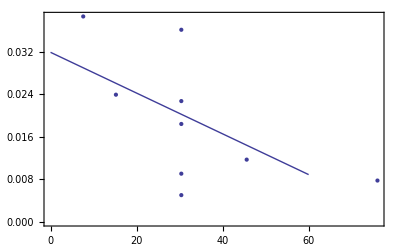

```mathematica
Show[ListPlot[data2],Plot[lm2[x],{x,0,60}],Frame->True]
```

```mathematica
lm2["RSquared"]
```

0.370901

```mathematica
Part C:
```

```mathematica
FOR THE NON-LINEAR REGRESSION CASE:
```

```mathematica
(*P ick the correct model *)
```

```mathematica
nlm3=NonlinearModelFit[data,A*Exp[B*x],{A,B},x]
```

FittedModel[3.5578×10^-35 ⅇ^(«19» x)]

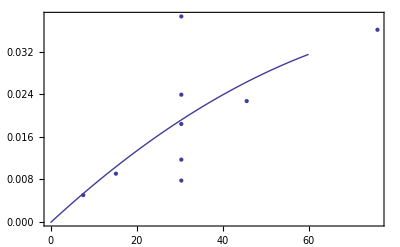

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,60}],Frame->True]
```

```mathematica
nlm=NonlinearModelFit[data,a*x^2+b*x+c,{a,b,c},x]
```

FittedModel[-0.000130281+«22» x-3.64047×10^-6 x^2]

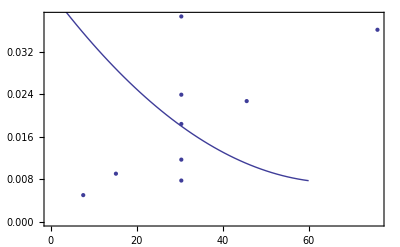

```mathematica
Show[ListPlot[data],Plot[nlm2[x],{x,0,60}],Frame->True]
```

```mathematica
nlm["RSquared"]
```

0.867049

```mathematica
nlm2=NonlinearModelFit[data2,a*x^2+b*x+c,{a,b,c},x]
```

FittedModel[0.0432161-«22» x+8.05979×10^-6 x^2]

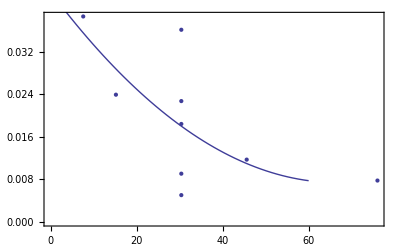

```mathematica
Show[ListPlot[data2],Plot[nlm2[x],{x,0,60}],Frame->True]
```

```mathematica
nlm4=NonlinearModelFit[data2,A*Exp[B*x],{A,B},x]
```

FittedModel[7.65763×10^-36 ⅇ^(«19» x)]

```mathematica
nlm2["RSquared"]
```

0.860347

```mathematica
The r-squared values for the non-linear fits for the plot of y against PCO and PN2O are both significantly higher than their linear analogues.
```

```mathematica
From their y-intercepts, 1/k1 can be determined.
```

```mathematica
From the linear fits:
```

```mathematica
1/0.00499805555555556;
```

200.078

```mathematica
1/.0318622
```

31.3852

```mathematica
From the non-linear fits:
```

```mathematica
Abs[1/0.000130281]
```

7675.72

```mathematica
N[Abs[1/.0432161],3]
```

23.1395

```mathematica
k1=N[(200+31+7675+23)/4,3]
```

1980.

```mathematica
There is clearly a discrepency here.
```

```mathematica
To determine K2, observe the slope of the Pn plot:
```

```mathematica
k2A=0.00043278508771929817*k1
```

0.857888

```mathematica
To determine k3, observe the slope of the Pc plot:
```

```mathematica
k3A=000382928*k1
```

7.59×10^8

```mathematica
Part D:
```

```mathematica
To determine which of the species are present on the surface in the greatest amount, simply look at equilibrium constance associated with surface site consing reaction steps.
```

```mathematica
Since k3 is larger than k2 and the deposrption of the produces N2 and CO2 is assumed to be fast relative to the eqilibrated steps, CO is the most abundent molecule on the surface.
```